# Rank-One Decomposition in Discrete Dipole Approximation

## 1. Basic Properties of metallic nanoparticles

#### Complex refractive index of materials

Reading and plotting the refractive index data for gold and silver metals. The refractive index data is downloaded from,
https://refractiveindex.info/
P. B. Johnson and R. W. Christy. Optical constants of the noble metals, Phys. Rev. B 6, 4370-4379 (1972)
The same refractive indices were used in the simulations using Discrete Dipole Method.

```mathematica
dataFolder=NotebookDirectory[]
```

/Users/abhisheksharma/Documents/Projects/Nanomaterials_Theory/Mathematica_Notebooks/

```mathematica
goldOptical=Import[dataFolder<>"Gold.csv","CSV"];
```

```mathematica
silverOptical=Import[dataFolder<>"Silver.csv","CSV"];
```

```mathematica
nGold=goldOptical⟦2;;201⟧;
kGold=goldOptical⟦204;;403⟧;
```

```mathematica
Length/@{nGold,kGold}
```

{200,200}

```mathematica
nSilver=silverOptical⟦2;;201⟧;
kSilver=silverOptical⟦204;;403⟧;
```

```mathematica
Length/@{nSilver,kSilver}
```

{200,200}

Plotting the refractive indices,

```mathematica
plot1=ListPlot[{nGold,kGold},PlotStyle->{{Red,Thickness[0.0125]},{Darker@Green,Thickness[0.0125]}},Joined-> True,Frame->True,FrameLabel-> {"Wavelength (μm)","n,k"},PlotLegends-> Placed[{"n","k"},{0.2,0.8}],PlotLabel-> "Refrative Index of Gold",AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ImageSize->200];
```

```mathematica
plot2=ListPlot[{nSilver,kSilver},PlotStyle->{{Red,Thickness[0.0125]},{Darker@Green,Thickness[0.0125]}},Joined-> True,Frame->True,FrameLabel-> {"Wavelength (μm)","n,k"},PlotLegends-> Placed[{"n","k"},{0.2,0.8}],PlotLabel-> "Refrative Index of Silver",AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ImageSize->200];
```

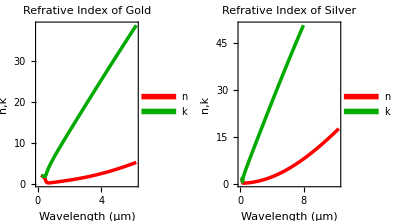

```mathematica
GraphicsRow[{plot1,plot2},ImageSize->400,Spacings-> 5]
```

```mathematica
Export[dataFolder<>"Gold_Ref_Index.png",plot1,ImageResolution-> 300]
Export[dataFolder<>"Silver_Ref_Index.png",plot2,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/Nanomaterials_Theory/Mathematica_Notebooks/Gold_Ref_Index.png

/Users/abhisheksharma/Documents/Projects/Nanomaterials_Theory/Mathematica_Notebooks/Silver_Ref_Index.png

Interpolating the refractive index coefficients, n, k for gold and silver.

```mathematica
intpnGold=Interpolation[nGold,InterpolationOrder->3]
```

InterpolatingFunction[…]

```mathematica
intpkGold=Interpolation[kGold,InterpolationOrder->3]
```

InterpolatingFunction[…]

```mathematica
intpnSilver=Interpolation[nSilver,InterpolationOrder->3]
```

InterpolatingFunction[…]

```mathematica
intpkSilver=Interpolation[kSilver,InterpolationOrder->3]
```

InterpolatingFunction[…]

```mathematica
mGold[λ_]=intpnGold[λ]+ⅈ intpkGold[λ];
```

```mathematica
mSilver[λ_]=intpnSilver[λ]+ⅈ intpkSilver[λ];
```

#### Basic Analysis and validity criteria

```mathematica
c=UnitConvert@Quantity["SpeedOfLight"]; (* Speed of Light *)
```

```mathematica
ϵ0=UnitConvert@Quantity["VacuumPermittivity"];(* Vacuum Permittivity *)
```

```mathematica
npLen=UnitConvert@Quantity[30,"nm"]; (* Characteristic Length of Nanoparticle *)
```

```mathematica
goldLC=UnitConvert[First@ElementData["Gold","LatticeConstants"],"nm"];
```

```mathematica
silverLC=UnitConvert[First@ElementData["Silver","LatticeConstants"],"nm"];
```

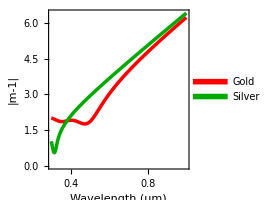

```mathematica
plot3=Plot[{Abs[mGold[λ]-1],Abs[mSilver[λ]-1]},{λ,0.3,1},PlotStyle->{{Red,Thickness[0.0125]},{Darker@Green,Thickness[0.0125]}},Frame->True,FrameLabel-> {"Wavelength (μm)","|m-1|"},PlotLegends-> Placed[{"Gold","Silver"},{0.2,0.8}],AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ImageSize->200]
```

```mathematica
Export[dataFolder<>"Validity_Criteria_1.png",plot3,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/Nanomaterials_Theory/Mathematica_Notebooks/Validity_Criteria_1.png

The validity criteria for the Discrete Dipole Approximation is valid are
|m|k d ≲ 1

m is the complex refractive of the material
k is wave number given by (2π)/λ
d is the dimension of volume of region equivalently described by the dipole
λ is the wavelength

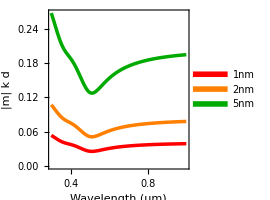

```mathematica
plot4=Plot[Evaluate[Abs[mGold[λ]](2π)/λ(# 10^-3)&/@{1,2,5}],{λ,0.3,1},PlotStyle->{{Red,Thickness[0.0125]},{Orange,Thickness[0.0125]},{Darker@Green,Thickness[0.0125]}},Frame->True,FrameLabel-> {"Wavelength (μm)","|m| k d"},PlotLegends-> Placed[LineLegend[{"1nm","2nm","5nm"},Spacings-> 0.1],{0.8,0.85}],AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ImageSize->200]
```

```mathematica
Export[dataFolder<>"Validity_Criteria_2.png",plot4,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/Nanomaterials_Theory/Mathematica_Notebooks/Validity_Criteria_2.png

With FCC structure, number of atoms in single dipole volume with size of length of dipole volume:

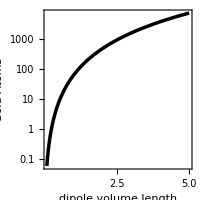

```mathematica
plot5=LogPlot[{4(Quantity[d,"nm"]/goldLC)^3},{d,0.1,5},PlotStyle->{Black,Thickness[0.0125]},Frame->True,FrameLabel-> {"dipole volume length","Gold Atoms"},AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ImageSize->200]
```

```mathematica
4(Quantity[2.5,"nm"]/goldLC)^3
```

921.456

```mathematica
Export[dataFolder<>"AtomicScaling.png",plot5,ImageResolution-> 300]
```

/Users/abhisheksharma/Documents/Projects/Nanomaterials_Theory/Mathematica_Notebooks/AtomicScaling.png

The dipole polarizability is given by using Clausius-Mossotti relationship,
α_j^CM= (3 d^3)/(4π)(ϵ_j-1)/(ϵ_j+2), 
where ϵ_j is the dielectric function and d^3 is the cubical sub-volume. 

Using the filtered coupled dipole method, the polarizability is given by,

α_j= 1/(1+ D)α_j^CM where,

D=α_j^CM/d^3[4/3(k d)^2+2/(3π)ln((π-k d)/(π + kd))(k d)^3 +2/3 ⅈ (k d)^3]

```mathematica
ϵGold[λ_]= mGold[λ]^2;
```

```mathematica
ϵSilver[λ_]=mSilver[λ]^2;
```

```mathematica
αCM[d_,ϵ_]:=(3 d^3)/(4π)(ϵ-1)/(ϵ+2)
```

```mathematica
αFCD[d_,ϵ_,λ_]=αCM[d,ϵ]/(1+FullSimplify[ 1/d^3 αCM[d,ϵ] (4/3(k d)^2+2/(3π)Log[(π-k d)/(π +k d)](k d)^3+2/3 ⅈ (k d)^3)/.k->(2π)/λ])
```

(3 d^3 (-1+ϵ))/(4 π (2+ϵ) (1+(4 d^2 π (-1+ϵ) (ⅈ d π+λ+d Log[1-(4 d)/(2 d+λ)]))/((2+ϵ) λ^3)))

```mathematica
UnitConvert[αCM[Quantity[#,"nm"],ϵGold[0.3]],"nm^3"]&/@{0.1,1,2.5,5}
```

{(0.000214758+0.000104958 ⅈ) nm^3,(0.214758+0.104958 ⅈ) nm^3,(3.3556+1.63997 ⅈ) nm^3,(26.8448+13.1198 ⅈ) nm^3}

```mathematica
αFCD[Quantity[#,"nm"],ϵGold[0.3],Quantity[500,"nm"]]&/@{0.1,1,2.5,5}
```

{(0.000214758+0.000104958 ⅈ) nm^3,(0.214751+0.104949 ⅈ) nm^3,(3.35489+1.63904 ⅈ) nm^3,(26.8226+13.0895 ⅈ) nm^3}

```mathematica
αType1=UnitConvert[αCM[Quantity[2.5,"nm"],ϵGold[0.3]],"nm^3"];
```

```mathematica
αType2=UnitConvert[αFCD[Quantity[2.5,"nm"],ϵGold[0.3],Quantity[500,"nm"]],"nm^3"];
```

```mathematica
{αType1,αType2}
```

{(3.3556+1.63997 ⅈ) nm^3,(3.35489+1.63904 ⅈ) nm^3}

### Polarization of a single dipole volume in electromagnetic field

Defining a electromagnetic radiation moving along Z axis. k vector given the direction of the propagation of the beam. The electric field vector for a moving electromagnetic wave along the z direction is given by,

```mathematica
k={k1,k2,k3}; (* Direction of input wave propagation along Z axis *)
```

```mathematica
NormK=Norm[k];(* Magnitude of the k vector *)
```

```mathematica
dipolePos={0,0,0}; (* Position of the dipole *)
```

```mathematica
EFieldX[r_]:=E0X ⅇ^(ⅈ k.r- ω t)
```

```mathematica
EFieldY[r_]:=E0Y ⅇ^(ⅈ k.r - ω t)
```

```mathematica
EFieldZ[r_]:=E0Z ⅇ^(ⅈ k.r - ω t)
```

```mathematica
EField[r_]={EFieldX[r],EFieldY[r],EFieldZ[r]}
```

{ⅇ^(-t ω+ⅈ {k1,k2,k3}.r) E0X,ⅇ^(-t ω+ⅈ {k1,k2,k3}.r) E0Y,ⅇ^(-t ω+ⅈ {k1,k2,k3}.r) E0Z}

Based on the first Maxwell’s equation, ∇.E=0

```mathematica
k.EField[r]== 0
```

ⅇ^(-t ω+ⅈ {k1,k2,k3}.r) E0X k1+ⅇ^(-t ω+ⅈ {k1,k2,k3}.r) E0Y k2+ⅇ^(-t ω+ⅈ {k1,k2,k3}.r) E0Z k3==0

So a vertical moving electromagnetic radiation k vector is  (for a given wavelength), its only possible if electric field vector along Z axis should be zero (Maxwell’s first equation). Also, as electric field and magnetic fields are also perpendicular to each other, we assume electric field is along x axis for the propagating electromagnetic radiation along Z axis.

```mathematica
k={0,0,(2π)/λ};
```

```mathematica
Solve[k.EField[r]== 0,E0Z]
```

{{E0Z→0}}

```mathematica
EField[z_,E0_]:={E0 ⅇ^(ⅈ (2π)/λ z),0,0}
```

```mathematica
α=UnitConvert[αCM[Quantity[2.5,"nm"],ϵGold[0.3]],"nm^3"];
```

```mathematica
Amat=Chop@QuantityMagnitude@(1/α IdentityMatrix[3]);Amat//MatrixForm
```

(0.240552-0.117565 ⅈ | 0 | 0
0 | 0.240552-0.117565 ⅈ | 0
0 | 0 | 0.240552-0.117565 ⅈ)

```mathematica
pol=Chop@FullSimplify@(Inverse[Amat].Transpose@{EField[0,1]});pol//MatrixForm
```

(3.3556+1.63997 ⅈ
0
0)

```mathematica
k={0,0,(2π)/λ};kNorm=Norm[k];
```

```mathematica
r={x,y,0};rNorm=Norm[r];
```

```mathematica
rD={0,0,0};
```

```mathematica
EScat[x_,y_,λ_]=Chop@FullSimplify[(kNorm^2 ⅇ^(ⅈ kNorm rNorm))/rNorm(ⅇ^(-ⅈ (k r/rNorm).rD)(Transpose[({r}/rNorm)].({r}/rNorm)-IdentityMatrix[3]).pol),Assumptions-> {λ>0,x>0,y>0}];EScat[x,y,λ]//MatrixForm
```

(-((132.474+64.7436 ⅈ) ⅇ^((2 ⅈ π √(x^2+y^2))/λ) y^2)/((x^2+y^2)^(3/2) λ^2)
((132.474+64.7436 ⅈ) ⅇ^((2 ⅈ π √(x^2+y^2))/λ) x y)/((x^2+y^2)^(3/2) λ^2)
0)

```mathematica
p1=DensityPlot[Abs@Re[EScat[x,y,300]]⟦1⟧,{x,-1,1},{y,-1,1},PlotRange-> {0,2 10^-2},MaxRecursion->15,ColorFunction->"SunsetColors",ImageSize->200,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},AspectRatio->1];
```

```mathematica
p2=DensityPlot[Abs@Re[EScat[x,y,300]]⟦2⟧,{x,-1,1},{y,-1,1},PlotRange-> {0,2 10^-2},MaxRecursion->15,ColorFunction->"SunsetColors",ImageSize->200,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},AspectRatio->1];
```

```mathematica
GraphicsRow[{p1,p2}]
```

-Graphics-

## 2. Dipole-Dipole Interaction in the presence of input electromagnetic radiation

### Creating generalized formulation of A matrix

```mathematica
ClearAll["Global`*"]
```

```mathematica
k={0,0,(2π)/λ};
```

```mathematica
kNorm=FullSimplify[Norm[k],Assumptions->{λ>0}];
```

```mathematica
Amat1[α_]:=1/α IdentityMatrix[3]
```

```mathematica
Amat2[{i_,j_},cList_:{}]:=Block[{dA,dB,r,rNorm},
If[Length@cList==0,
dA={Symbol["x"<>ToString[i]],Symbol["y"<>ToString[i]],Symbol["z"<>ToString[i]]};
dB={Symbol["x"<>ToString[j]],Symbol["y"<>ToString[j]],Symbol["z"<>ToString[j]]},
dA=cList⟦1⟧;dB=cList⟦2⟧];
r={(dA-dB)};
rNorm=FullSimplify[Norm[r],Assumptions->Flatten@{dA,dB}∈Reals];Evaluate[ⅇ^(ⅈ kNorm rNorm)/rNorm(kNorm^2(Transpose[(r/rNorm)].(r/rNorm)-IdentityMatrix[3])+(ⅈ kNorm rNorm-1)/rNorm^2(3 Transpose[(r/rNorm)].(r/rNorm)-IdentityMatrix[3]))]//FullSimplify]
```

```mathematica
Amat[{i_,j_},α_,cList_:{}]:=If[i==j,Amat1[α],Amat2[{i,j},cList]]
```

Calculating total A matrix assuming polarizability α of all the dipoles is same.

```mathematica
AmatTotal[nD_,α_,dipolesList_:{}]:=Block[{dipolepairList={},indexList},
If[Length@dipolesList≠0,
indexList=Table[{i,j},{i,Length@dipolesList},{j,Length@dipolesList}];
dipolepairList=Table[{dipolesList⟦i⟧,dipolesList⟦j⟧},{i,Length@dipolesList},{j,Length@dipolesList}];
ArrayReshape[ArrayFlatten@Table[Amat[indexList⟦i,j⟧,α,dipolepairList⟦i,j⟧],{i,nD},{j,nD}],{3nD,3nD}],
ArrayReshape[ArrayFlatten@Table[Amat[{i,j},α],{i,nD},{j,nD}],{3nD,3nD}]]];
```

The A matrix for two dipoles is given by with polarizability defined by Clausius-Mossotti relationship

```mathematica
AmatT = FullSimplify[AmatTotal[2,α,{{0,0,0},{m,0,0}}]/.α->(3 d^3)/(4π)(ϵ-1)/(ϵ+2)/.m->d,Assumptions->{d∈Reals, d>0}];AmatT//MatrixForm
```

((4 π (2+ϵ))/(3 d^3 (-1+ϵ)) | 0 | 0 | (2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0
0 | (4 π (2+ϵ))/(3 d^3 (-1+ϵ)) | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0
0 | 0 | (4 π (2+ϵ))/(3 d^3 (-1+ϵ)) | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2)
(2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0 | (4 π (2+ϵ))/(3 d^3 (-1+ϵ)) | 0 | 0
0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | (4 π (2+ϵ))/(3 d^3 (-1+ϵ)) | 0
0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | (4 π (2+ϵ))/(3 d^3 (-1+ϵ)))

Inverting A Matrix and simplifying

```mathematica
AmatTInv=FullSimplify@Inverse[AmatT];AmatTInv//MatrixForm
```

(1/((4 π (2+ϵ))/(3 d^3 (-1+ϵ))+(3 ⅇ^((4 ⅈ d π)/λ) (-1+ϵ) (2 d π+ⅈ λ)^2)/(d^3 π (2+ϵ) λ^2)) | 0 | 0 | 1/((2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ)+(8 ⅇ^(-(2 ⅈ d π)/λ) π^2 (2+ϵ)^2 λ)/(9 d^3 (-1+ϵ)^2 (-2 ⅈ d π+λ))) | 0 | 0
0 | 1/((4 π (2+ϵ))/(3 d^3 (-1+ϵ))-(3 ⅇ^((4 ⅈ d π)/λ) (-1+ϵ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(4 d^3 π (2+ϵ) λ^4)) | 0 | 0 | (9 d^3 ⅇ^((2 ⅈ d π)/λ) λ^2)/((16 π^2 (2+ϵ)^2 λ^4)/((-1+ϵ)^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))+9 ⅇ^((4 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2)) | 0
0 | 0 | 1/((4 π (2+ϵ))/(3 d^3 (-1+ϵ))-(3 ⅇ^((4 ⅈ d π)/λ) (-1+ϵ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(4 d^3 π (2+ϵ) λ^4)) | 0 | 0 | (9 d^3 ⅇ^((2 ⅈ d π)/λ) λ^2)/((16 π^2 (2+ϵ)^2 λ^4)/((-1+ϵ)^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))+9 ⅇ^((4 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))
1/((2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ)+(8 ⅇ^(-(2 ⅈ d π)/λ) π^2 (2+ϵ)^2 λ)/(9 d^3 (-1+ϵ)^2 (-2 ⅈ d π+λ))) | 0 | 0 | 1/((4 π (2+ϵ))/(3 d^3 (-1+ϵ))+(3 ⅇ^((4 ⅈ d π)/λ) (-1+ϵ) (2 d π+ⅈ λ)^2)/(d^3 π (2+ϵ) λ^2)) | 0 | 0
0 | (9 d^3 ⅇ^((2 ⅈ d π)/λ) λ^2)/((16 π^2 (2+ϵ)^2 λ^4)/((-1+ϵ)^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))+9 ⅇ^((4 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2)) | 0 | 0 | 1/((4 π (2+ϵ))/(3 d^3 (-1+ϵ))-(3 ⅇ^((4 ⅈ d π)/λ) (-1+ϵ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(4 d^3 π (2+ϵ) λ^4)) | 0
0 | 0 | (9 d^3 ⅇ^((2 ⅈ d π)/λ) λ^2)/((16 π^2 (2+ϵ)^2 λ^4)/((-1+ϵ)^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))+9 ⅇ^((4 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2)) | 0 | 0 | 1/((4 π (2+ϵ))/(3 d^3 (-1+ϵ))-(3 ⅇ^((4 ⅈ d π)/λ) (-1+ϵ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(4 d^3 π (2+ϵ) λ^4)))

The scattered electric field at a given point is given by:

```mathematica
EScat[pol_,rD_,r_]:=Block[{rNorm},rNorm=Norm[r];(kNorm^2 ⅇ^(ⅈ kNorm rNorm))/rNorm(∑_(j=1)^(Length@pol) ⅇ^(-ⅈ (k r/rNorm).rD⟦j⟧)(Transpose[({r}/rNorm)].({r}/rNorm)-IdentityMatrix[3]).pol⟦j⟧)]
```

## 3. Example Matrix Formulation on 1/2/3 dimensional array of dipoles

#### One dimensional array of dipoles

```mathematica
plotParams={LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->10]},ImageSize->Small};
```

```mathematica
dipoles1D={#,0,0}&/@Range[-10,10];
```

```mathematica
Show[{RegionPlot3D[Region[Cube[dipoles1D[[#]],1]],ViewProjection->"Orthographic",ViewPoint->{0,0,Infinity},PlotStyle->Directive[Yellow,Opacity[0.25]],Mesh->None]&/@Range[Length@dipoles1D],ListPointPlot3D[dipoles1D,PlotStyle->Black]},ImageSize->500]
```

-Graphics3D-

```mathematica
Graphics3D[{Yellow,Specularity[White,10],Sphere[dipoles1D,0.2]},ViewPoint->Front,ImageSize->500]
```

-Graphics3D-

```mathematica
params={λ-> 300,α-> 0.1(1+ⅈ)}; (* Test Values*)
```

```mathematica
A=AmatTotal[Length@dipoles1D,α,dipoles1D]/.params;
```

The matrix structure of A looks like,

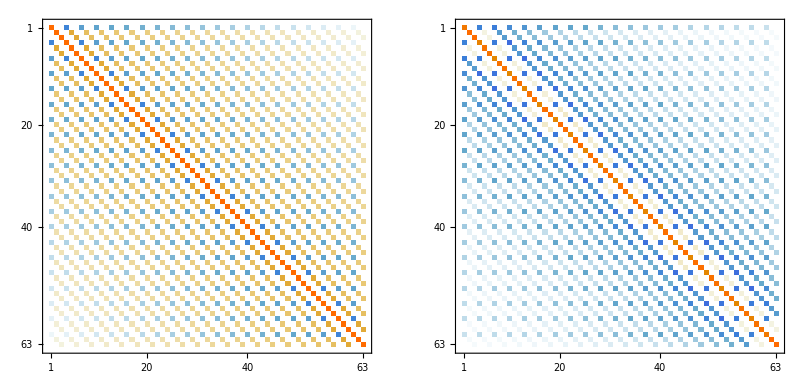

```mathematica
GraphicsRow@{MatrixPlot[N@A,plotParams],MatrixPlot[Inverse[N@A],plotParams]}
```

```mathematica
EField=Transpose@{Flatten@({ⅇ^(ⅈ k.#),0,0}/.params&/@dipoles1D)};
```

```mathematica
pol=Chop@Partition[Flatten@FullSimplify[Inverse[N@A].EField],3];pol
```

{{0.0605032+0.155459 ⅈ,0,0},{0.0365831+0.196489 ⅈ,0,0},{0.0198797+0.203568 ⅈ,0,0},{0.0125516+0.202789 ⅈ,0,0},{0.00986728+0.201343 ⅈ,0,0},{0.00894675+0.200475 ⅈ,0,0},{0.0086043+0.20007 ⅈ,0,0},{0.00844339+0.199899 ⅈ,0,0},{0.00835139+0.199829 ⅈ,0,0},{0.00830034+0.199801 ⅈ,0,0},{0.00828373+0.199793 ⅈ,0,0},{0.00830034+0.199801 ⅈ,0,0},{0.00835139+0.199829 ⅈ,0,0},{0.00844339+0.199899 ⅈ,0,0},{0.0086043+0.20007 ⅈ,0,0},{0.00894675+0.200475 ⅈ,0,0},{0.00986728+0.201343 ⅈ,0,0},{0.0125516+0.202789 ⅈ,0,0},{0.0198797+0.203568 ⅈ,0,0},{0.0365831+0.196489 ⅈ,0,0},{0.0605032+0.155459 ⅈ,0,0}}

#### Two dimensional array of dipoles

```mathematica
dipoles2D=Flatten[Table[{i,j,0},{i,-2,2},{j,-2,2}],1];
```

```mathematica
Show[{RegionPlot3D[Region[Cube[dipoles2D[[#]],1]],ViewProjection->"Orthographic",PlotStyle->Directive[Yellow,Opacity[0.25]],Mesh->None]&/@Range[Length@dipoles2D],ListPointPlot3D[dipoles2D,PlotStyle->Black]},ImageSize->200]
```

-Graphics3D-

```mathematica
Graphics3D[{Yellow,Specularity[White,10],Sphere[dipoles2D,0.2]},ViewPoint->Top,ImageSize->200]
```

-Graphics3D-

```mathematica
A=AmatTotal[Length@dipoles2D,α,dipoles2D]/.params;
```

The matrix structure of A looks like,

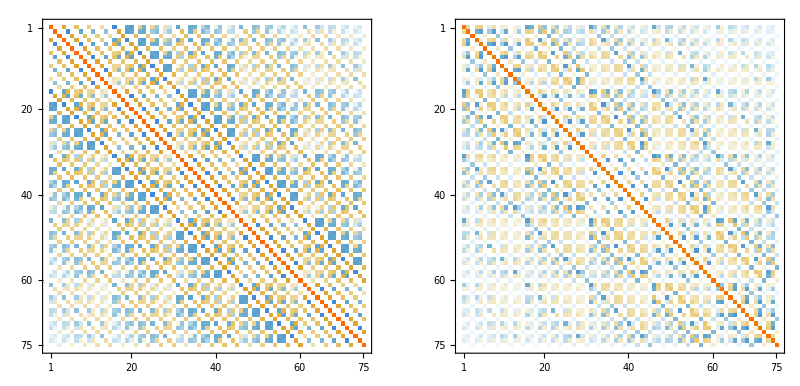

```mathematica
GraphicsRow@{MatrixPlot[N@A,plotParams],MatrixPlot[Inverse[N@A],plotParams]}
```

```mathematica
EField=Transpose@{Flatten@({ⅇ^(ⅈ k.#),0,0}/.params&/@dipoles2D)};
```

```mathematica
Partition[Flatten@FullSimplify[Inverse[N@A].EField],3]//MatrixForm;
```

#### Testing three dimensional array of dipoles

```mathematica
dipoles3D=Flatten[Table[{i,j,k},{i,-1,1},{j,-1,1},{k,-1,1}],2];
```

```mathematica
Show[{RegionPlot3D[Region[Cube[dipoles3D[[#]],1]],ViewProjection->"Orthographic",PlotStyle->Directive[Yellow,Opacity[0.25]],Mesh->None]&/@Range[Length@dipoles3D],ListPointPlot3D[dipoles3D,PlotStyle->Black]},ImageSize->200]
```

-Graphics3D-

```mathematica
Graphics3D[{Yellow,Specularity[White,10],Sphere[dipoles3D,0.2]},ViewPoint->{1.5,1,1},ViewProjection->"Orthographic",ImageSize->200]
```

-Graphics3D-

```mathematica
A=AmatTotal[Length@dipoles3D,α,dipoles3D]/.params;
```

The matrix structure of A looks like,

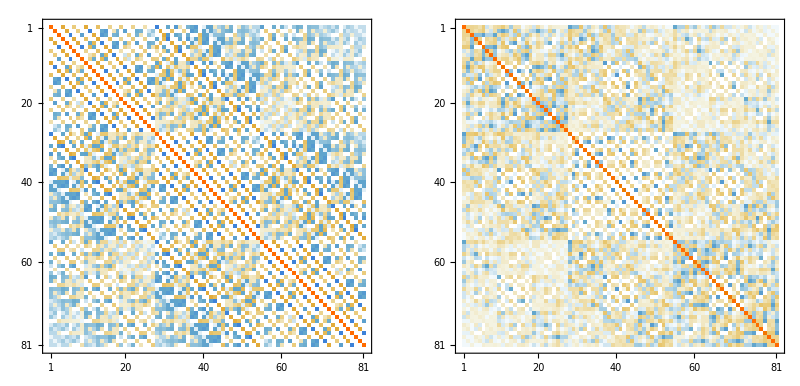

```mathematica
GraphicsRow@{MatrixPlot[N@A,plotParams],MatrixPlot[Inverse[N@A],plotParams]}
```

## 4. Rank One Decomposition Method : Updating the polarizability of dipole

In this section, we demonstrate the implementation of Rank One Decomposition Method to demonstrate the efficient computational method to investigate nanomaterials growth and etching process. In this section, we setup an example describing updating the A matrix when the polarizability of a dipole is updated. We will compare the direct solution and using rank-one decomposition method. Consider three dipoles at positions, {{0,0,0}, {m,0,0},{0,m,0}}.

```mathematica
ClearAll["Global`*"]
```

```mathematica
k={0,0,(2π)/λ};
```

```mathematica
kNorm=FullSimplify[Norm[k],Assumptions->{λ>0}];
```

```mathematica
Amat1[{i_},α_]:=1/α IdentityMatrix[3]
```

```mathematica
Amat2[{i_,j_},cList_:{}]:=Block[{dA,dB,r,rNorm},
If[Length@cList==0,
dA={Symbol["x"<>ToString[i]],Symbol["y"<>ToString[i]],Symbol["z"<>ToString[i]]};
dB={Symbol["x"<>ToString[j]],Symbol["y"<>ToString[j]],Symbol["z"<>ToString[j]]},
dA=cList⟦1⟧;dB=cList⟦2⟧];
r={(dA-dB)};
rNorm=FullSimplify[Norm[r],Assumptions->Flatten@{dA,dB}∈Reals];Evaluate[ⅇ^(ⅈ kNorm rNorm)/rNorm(kNorm^2(Transpose[(r/rNorm)].(r/rNorm)-IdentityMatrix[3])+(ⅈ kNorm rNorm-1)/rNorm^2(3 Transpose[(r/rNorm)].(r/rNorm)-IdentityMatrix[3]))]//FullSimplify]
```

```mathematica
Amat[{i_,j_},α_,cList_:{}]:=If[i==j,Amat1[{i},α],Amat2[{i,j},cList]]
```

Calculating total A matrix assuming polarizability α of all the dipoles is same.

```mathematica
AmatTotal[nD_,αList_,dipolesList_:{}]:=Block[{dipolepairList={},indexList},
If[Length@dipolesList≠0,
indexList=Table[{i,j},{i,Length@dipolesList},{j,Length@dipolesList}];
dipolepairList=Table[{dipolesList⟦i⟧,dipolesList⟦j⟧},{i,Length@dipolesList},{j,Length@dipolesList}];
ArrayReshape[ArrayFlatten@Table[Amat[indexList⟦i,j⟧,αList[[i]],dipolepairList⟦i,j⟧],{i,nD},{j,nD}],{3nD,3nD}],
ArrayReshape[ArrayFlatten@Table[Amat[{i,j},αList[[i]]],{i,nD},{j,nD}],{3nD,3nD}]]];
```

The A matrix for two dipoles of same polarizability α_1, which defines the initial A matrix and its inverse is given by

```mathematica
AmatInit=FullSimplify[AmatTotal[2,{α1,α1},{{0,0,0},{m,0,0}}]/.m->d,Assumptions->{d∈Reals, d>0}];AmatInit//MatrixForm
```

(1/α1 | 0 | 0 | (2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0
0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0
0 | 0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2)
(2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0 | 1/α1 | 0 | 0
0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α1 | 0
0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α1)

The inverse of A matrix which is used as initial solution when the polarizability is updated.

```mathematica
AmatInitInv=FullSimplify@Inverse[AmatInit];AmatInitInv//MatrixForm
```

(1/(1/α1+(4 ⅇ^((4 ⅈ d π)/λ) α1 (2 d π+ⅈ λ)^2)/(d^6 λ^2)) | 0 | 0 | -(2 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2+d^6 λ^2) | 0 | 0
0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0
0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)
-(2 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2+d^6 λ^2) | 0 | 0 | 1/(1/α1+(4 ⅇ^((4 ⅈ d π)/λ) α1 (2 d π+ⅈ λ)^2)/(d^6 λ^2)) | 0 | 0
0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0
0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)))

Consider the case when the property of the second dipole is changed from α_1 to α_2, in that case the updated matrix using direct method is given by,

```mathematica
AmatDirect=FullSimplify[AmatTotal[2,{α1,α2},{{0,0,0},{m,0,0}}]/.m->d,Assumptions->{d∈Reals, d>0}];AmatDirect//MatrixForm
```

(1/α1 | 0 | 0 | (2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0
0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0
0 | 0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2)
(2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0 | 1/α2 | 0 | 0
0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α2 | 0
0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α2)

and, the inverted A matrix for the new solution is given by,

```mathematica
AmatDirectInv=FullSimplify@Inverse[AmatDirect];AmatDirectInv//MatrixForm
```

(1/(1/α1+(4 ⅇ^((4 ⅈ d π)/λ) α2 (2 d π+ⅈ λ)^2)/(d^6 λ^2)) | 0 | 0 | -(2 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1 α2 (2 d π+ⅈ λ) λ)/(4 ⅇ^((4 ⅈ d π)/λ) α1 α2 (2 d π+ⅈ λ)^2+d^6 λ^2) | 0 | 0
0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1 α2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 α2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0
0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1 α2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 α2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)
-(2 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1 α2 (2 d π+ⅈ λ) λ)/(4 ⅇ^((4 ⅈ d π)/λ) α1 α2 (2 d π+ⅈ λ)^2+d^6 λ^2) | 0 | 0 | 1/(1/α2+(4 ⅇ^((4 ⅈ d π)/λ) α1 (2 d π+ⅈ λ)^2)/(d^6 λ^2)) | 0 | 0
0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1 α2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 α2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0 | 1/(1/α2-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0
0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1 α2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 α2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0 | 1/(1/α2-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)))

To demonstrate the rank-one decomposition method : If A and (A+B) are invertible, and B has rank one, then let g=tr(BA^-1). If g≠-1, we have (A+B)^-1=A^-1-1/(1+g)A^-1 B A^-1.

Here, A_updated^-1=(A_init+B)^-1=A_init^-1-1/(1+g)A_init^-1 B A_init^-1, where A_init is the initial solution and B matrix updates the polarizability along each axis sequentially. 
The B matrices along X, Y, and Z are given by

```mathematica
B1=ConstantArray[0,{6,6}];B1[[4,4]]=-1/α1+1/α2;
B2=ConstantArray[0,{6,6}];B2[[5,5]]=-1/α1+1/α2;
B3=ConstantArray[0,{6,6}];B3[[6,6]]=-1/α1+1/α2;
```

The A matrix for updated polarizability can be described as A_updated= A_init+ B_1+B_2+B_3. Checking, if they are equal

```mathematica
AmatDirect==AmatInit+B1+B2+B3
```

True

Using the rank-one decomposition, the inverted solution can be defined as,

```mathematica
invSum[iA_,B_]:=iA - 1/(1+Tr[B . iA]) Evaluate@(iA .B .iA)
```

Updating the inverted matrix for change in polarizability along X

```mathematica
stepX=FullSimplify@invSum[FullSimplify@Inverse[AmatInit],B1]; (* Step X *)
```

Updating the inverted matrix for change in polarizability along Y

```mathematica
stepY=FullSimplify@invSum[stepX,B2]; (* Step Y *)
```

Updating the inverted matrix for change in polarizability along Z

```mathematica
AmatRankOneInv=FullSimplify@invSum[stepY,B3]; (* Step Z*)
```

The final inverted matrix from rank-one decomposition method is,

```mathematica
AmatRankOneInv//MatrixForm
```

(1/(1/α1+(4 ⅇ^((4 ⅈ d π)/λ) α2 (2 d π+ⅈ λ)^2)/(d^6 λ^2)) | 0 | 0 | -(2 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1 α2 (2 d π+ⅈ λ) λ)/(4 ⅇ^((4 ⅈ d π)/λ) α1 α2 (2 d π+ⅈ λ)^2+d^6 λ^2) | 0 | 0
0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1 α2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 α2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0
0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1 α2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 α2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)
-(2 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1 α2 (2 d π+ⅈ λ) λ)/(4 ⅇ^((4 ⅈ d π)/λ) α1 α2 (2 d π+ⅈ λ)^2+d^6 λ^2) | 0 | 0 | 1/(1/α2+(4 ⅇ^((4 ⅈ d π)/λ) α1 (2 d π+ⅈ λ)^2)/(d^6 λ^2)) | 0 | 0
0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1 α2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 α2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0 | 1/(1/α2-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0
0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1 α2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 α2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0 | 1/(1/α2-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)))

Checking if the inverted matrices from direct solution and rank-one decomposition method are equivalent,

```mathematica
AmatRankOneInv==AmatDirectInv
```

True

and  A A^-1= I

```mathematica
FullSimplify[AmatDirect. AmatRankOneInv]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

## 5. Rank One Decomposition Method : Adding a new dipole

We start with considering a case when two dipoles is present at {{0, 0, 0}, {m, 0, 0}} and a new dipole is added at {2m, 0, 0}. Assuming all dipoles have same polarizability α, the initial A matrix and its inverse for the first dipoles is given by,

```mathematica
AmatInit=FullSimplify[AmatTotal[2,{α1,α1},{{0,0,0},{m,0,0}}]/.m->d,Assumptions->{d∈Reals, d>0}];AmatInit//MatrixForm
```

(1/α1 | 0 | 0 | (2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0
0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0
0 | 0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2)
(2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0 | 1/α1 | 0 | 0
0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α1 | 0
0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α1)

```mathematica
AmatInitInv=FullSimplify[Inverse@AmatInit];AmatInitInv//MatrixForm
```

(1/(1/α1+(4 ⅇ^((4 ⅈ d π)/λ) α1 (2 d π+ⅈ λ)^2)/(d^6 λ^2)) | 0 | 0 | -(2 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2+d^6 λ^2) | 0 | 0
0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0
0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)
-(2 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2+d^6 λ^2) | 0 | 0 | 1/(1/α1+(4 ⅇ^((4 ⅈ d π)/λ) α1 (2 d π+ⅈ λ)^2)/(d^6 λ^2)) | 0 | 0
0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0
0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)))

Considering a new dipole added at {m, 0, 0} with polarizability α1, the updated A matrix and its inverse is given by

```mathematica
AmatUpdated=FullSimplify[AmatTotal[3,{α1,α1,α1},{{0,0,0},{m,0,0},{2m,0,0}}]/.m->d,Assumptions->{d∈Reals, d>0}];AmatUpdated//MatrixForm
```

(1/α1 | 0 | 0 | (2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0 | (ⅇ^((4 ⅈ d π)/λ) (4 ⅈ d π-λ))/(4 d^3 λ) | 0 | 0
0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | (ⅇ^((4 ⅈ d π)/λ) (-16 d^2 π^2-4 ⅈ d π λ+λ^2))/(8 d^3 λ^2) | 0
0 | 0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | (ⅇ^((4 ⅈ d π)/λ) (-16 d^2 π^2-4 ⅈ d π λ+λ^2))/(8 d^3 λ^2)
(2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0 | 1/α1 | 0 | 0 | (2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0
0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0
0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2)
(ⅇ^((4 ⅈ d π)/λ) (4 ⅈ d π-λ))/(4 d^3 λ) | 0 | 0 | (2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0 | 1/α1 | 0 | 0
0 | (ⅇ^((4 ⅈ d π)/λ) (-16 d^2 π^2-4 ⅈ d π λ+λ^2))/(8 d^3 λ^2) | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α1 | 0
0 | 0 | (ⅇ^((4 ⅈ d π)/λ) (-16 d^2 π^2-4 ⅈ d π λ+λ^2))/(8 d^3 λ^2) | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α1)

The direct solution of the inverse of A matrix with three dipoles,

```mathematica
AmatUpdatedInv=FullSimplify[Inverse[AmatUpdated]];AmatUpdatedInv//MatrixForm
```

((64 ⅈ d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 (2 d π+ⅈ λ)^2 λ+16 ⅈ d^9 α1 λ^3)/(128 ⅈ d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 ⅈ d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (4 d π+ⅈ λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | -(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | (4 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ (-64 d^2 π^2 α1-4 ⅈ d π (d^3+16 α1) λ+(d^3+16 α1) λ^2))/(128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (-4 ⅈ d π+λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0
0 | (64 d^9 α1 λ^6-64 d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(64 d^9 λ^6-128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2-ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (128 d^4 π^4 α1+128 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-6 α1) λ^2+4 ⅈ d π (d^3-8 α1) λ^3-(d^3-8 α1) λ^4))/(-64 d^9 λ^6+128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2+ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0
0 | 0 | (64 d^9 α1 λ^6-64 d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(64 d^9 λ^6-128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2-ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (128 d^4 π^4 α1+128 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-6 α1) λ^2+4 ⅈ d π (d^3-8 α1) λ^3-(d^3-8 α1) λ^4))/(-64 d^9 λ^6+128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2+ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4))
-(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | (d^3 α1 λ (ⅈ ⅇ^((4 ⅈ d π)/λ) α1 (4 d π+ⅈ λ)+4 d^3 λ))/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | -(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0
0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | (d^3 α1 λ^2 (8 d^3 λ^2-ⅇ^((4 ⅈ d π)/λ) α1 (16 d^2 π^2+4 ⅈ d π λ-λ^2)))/(8 d^6 λ^4-ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0
0 | 0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | (d^3 α1 λ^2 (8 d^3 λ^2-ⅇ^((4 ⅈ d π)/λ) α1 (16 d^2 π^2+4 ⅈ d π λ-λ^2)))/(8 d^6 λ^4-ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4))
(4 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ (-64 d^2 π^2 α1-4 ⅈ d π (d^3+16 α1) λ+(d^3+16 α1) λ^2))/(128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (-4 ⅈ d π+λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | -(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | (64 ⅈ d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 (2 d π+ⅈ λ)^2 λ+16 ⅈ d^9 α1 λ^3)/(128 ⅈ d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 ⅈ d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (4 d π+ⅈ λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0
0 | -(8 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (128 d^4 π^4 α1+128 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-6 α1) λ^2+4 ⅈ d π (d^3-8 α1) λ^3-(d^3-8 α1) λ^4))/(-64 d^9 λ^6+128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2+ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | (64 d^9 α1 λ^6-64 d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(64 d^9 λ^6-128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2-ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0
0 | 0 | -(8 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (128 d^4 π^4 α1+128 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-6 α1) λ^2+4 ⅈ d π (d^3-8 α1) λ^3-(d^3-8 α1) λ^4))/(-64 d^9 λ^6+128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2+ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | (64 d^9 α1 λ^6-64 d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(64 d^9 λ^6-128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2-ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)))

Starting with the  A matrix of the two dipole case, the updated matrix for three dipoles is given by,

```mathematica
AmatN=Table[ToExpression["A"<>ToString[i]<>ToString[j]],{i,9},{j,9}];Table[AmatN[[i,j]]=AmatInit[[i,j]],{i,Length@AmatInit},{j,Length@AmatInit}];
Table[AmatN[[i,j]]=0,{i,7,9},{j,7,9}];
Table[AmatN[[i,i]]=1/α1,{i,7,9}];
AmatN//MatrixForm
```

(1/α1 | 0 | 0 | (2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0 | A17 | A18 | A19
0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | A27 | A28 | A29
0 | 0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | A37 | A38 | A39
(2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0 | 1/α1 | 0 | 0 | A47 | A48 | A49
0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α1 | 0 | A57 | A58 | A59
0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α1 | A67 | A68 | A69
A71 | A72 | A73 | A74 | A75 | A76 | 1/α1 | 0 | 0
A81 | A82 | A83 | A84 | A85 | A86 | 0 | 1/α1 | 0
A91 | A92 | A93 | A94 | A95 | A96 | 0 | 0 | 1/α1)

Here, all the coefficients A<i><j> are known from the A matrix for 3x3 dipoles. Starting with the inverted A matrix for the two dipoles, the inverted matrix for three dipoles can be created in three steps by adding single row and column at a time. For a single row and column addition, generating part of A matrix without considering dipole-dipole interactions,

```mathematica
auxA=ConstantArray[0,{7,7}];Table[auxA[[i,j]]=AmatInit[[i,j]],{i,Length@AmatInit},{j,Length@AmatInit}];auxA[[7,7]]=1/α1;auxA//MatrixForm;
```

```mathematica
AmatauxinvRankOne=ConstantArray[0,{7,7}];Table[AmatauxinvRankOne[[i,j]]=AmatInitInv[[i,j]],{i,Length@AmatInitInv},{j,Length@AmatInitInv}];AmatauxinvRankOne[[7,7]]=α1;AmatauxinvRankOne//MatrixForm
```

(1/(1/α1+(4 ⅇ^((4 ⅈ d π)/λ) α1 (2 d π+ⅈ λ)^2)/(d^6 λ^2)) | 0 | 0 | -(2 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2+d^6 λ^2) | 0 | 0 | 0
0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0
0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0
-(2 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2+d^6 λ^2) | 0 | 0 | 1/(1/α1+(4 ⅇ^((4 ⅈ d π)/λ) α1 (2 d π+ⅈ λ)^2)/(d^6 λ^2)) | 0 | 0 | 0
0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0
0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0
0 | 0 | 0 | 0 | 0 | 0 | α1)

The dipole-dipole interactions are adding by adding a single row and column matrix, which could be defined by B1 and B2. And, hence single row and column addition is defined by A_int= auxA+B1+B2.

```mathematica
B=ConstantArray[0,{7,7}]; Table[B[[7,i]]=AmatUpdated[[7,i]],{i,6}];
B1=B;B2=Transpose[B];
```

```mathematica
(auxA+B1+B2)//MatrixForm
```

(1/α1 | 0 | 0 | (2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0 | (ⅇ^((4 ⅈ d π)/λ) (4 ⅈ d π-λ))/(4 d^3 λ)
0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0
0 | 0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0
(2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0 | 1/α1 | 0 | 0 | (2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ)
0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α1 | 0 | 0
0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α1 | 0
(ⅇ^((4 ⅈ d π)/λ) (4 ⅈ d π-λ))/(4 d^3 λ) | 0 | 0 | (2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0 | 1/α1)

To calculate the inverse of the A_int matrix, we update the solution using rank-one decomposition method in two steps.

```mathematica
invSum[iA_,B_]:=iA - 1/(1+Tr[B . iA])iA .B .iA
```

Hence, the solution of single step can be defined by,

```mathematica
singleStepInverse=FullSimplify[invSum[invSum[AmatauxinvRankOne,B1],B2],Assumptions->{λ∈Reals,d∈Reals}];
```

```mathematica
singleStepInverse//MatrixForm
```

((64 d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 (2 d π+ⅈ λ)^2 λ+16 d^9 α1 λ^3)/(128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (-4 ⅈ d π+λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | -(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | (4 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ (-64 d^2 π^2 α1-4 ⅈ d π (d^3+16 α1) λ+(d^3+16 α1) λ^2))/(128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (-4 ⅈ d π+λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2))
0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0
0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0
-(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | (d^3 α1 λ (ⅈ ⅇ^((4 ⅈ d π)/λ) α1 (4 d π+ⅈ λ)+4 d^3 λ))/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | -(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2))
0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0
0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0
(4 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ (-64 d^2 π^2 α1-4 ⅈ d π (d^3+16 α1) λ+(d^3+16 α1) λ^2))/(128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (-4 ⅈ d π+λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | -(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | (64 d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 (2 d π+ⅈ λ)^2 λ+16 d^9 α1 λ^3)/(128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (-4 ⅈ d π+λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)))

To check the validity of single step solution,  we show A_int A_singleStep=I, where I is the identity matrix

```mathematica
FullSimplify[singleStepInverse.(auxA+B1+B2)]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
FullSimplify[singleStepInverse.(auxA+B1+B2)]==IdentityMatrix[7]
```

True

Using the strategy as described above, here we start with the initial inverse A matrix of two dipoles and update the inverse matrix for the three dipole system in three consecutive steps. (from 6×6 matrix to 9×9)

```mathematica
(* STEP 1: Updating the first row and column *)
auxA=ConstantArray[0,{7,7}];Table[auxA[[i,j]]=AmatUpdated[[i,j]],{i,6},{j,6}];auxA[[7,7]]=1/α1;
```

```mathematica
auxMat=AmatInitInv;
len=Length@auxMat;
AmatauxinvRankOne=ConstantArray[0,{len+1,len+1}];
AmatauxinvRankOne[[len+1,len+1]]=α1;
Table[AmatauxinvRankOne[[i,j]]=auxMat[[i,j]],{i,len},{j,len}];
B=ConstantArray[0,{len+1,len+1}]; Table[B[[len+1,i]]=AmatUpdated[[len+1,i]],{i,len}];
B1=B;B2=Transpose[B];
auxUpdate=FullSimplify[invSum[invSum[AmatauxinvRankOne,B1],B2],Assumptions->{λ∈Reals,d∈Reals}];
FullSimplify[(auxA+B1+B2).auxUpdate]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(* STEP 2: Updating the second row and column *)
auxA=ConstantArray[0,{8,8}];Table[auxA[[i,j]]=AmatUpdated[[i,j]],{i,7},{j,7}];auxA[[8,8]]=1/α1;
auxMat=auxUpdate;
len=Length@auxMat;
AmatauxinvRankOne=ConstantArray[0,{len+1,len+1}];
AmatauxinvRankOne[[len+1,len+1]]=α1;
Table[AmatauxinvRankOne[[i,j]]=auxMat[[i,j]],{i,len},{j,len}];
B=ConstantArray[0,{len+1,len+1}]; Table[B[[len+1,i]]=AmatUpdated[[len+1,i]],{i,len}];
B1=B;B2=Transpose[B];
auxUpdate=invSum[invSum[AmatauxinvRankOne,B1],B2];
FullSimplify[(auxA+B1+B2).auxUpdate]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(* STEP 3: Updating the third row and column *)
```

```mathematica
auxA=ConstantArray[0,{9,9}];Table[auxA[[i,j]]=AmatUpdated[[i,j]],{i,8},{j,8}];auxA[[9,9]]=1/α1;
auxMat=auxUpdate;
len=Length@auxMat;
AmatauxinvRankOne=ConstantArray[0,{len+1,len+1}];
AmatauxinvRankOne[[len+1,len+1]]=α1;
Table[AmatauxinvRankOne[[i,j]]=auxMat[[i,j]],{i,len},{j,len}];
B=ConstantArray[0,{len+1,len+1}]; Table[B[[len+1,i]]=AmatUpdated[[len+1,i]],{i,len}];
B1=B;B2=Transpose[B];
auxUpdate=invSum[invSum[AmatauxinvRankOne,B1],B2];
FullSimplify[(auxA+B1+B2).auxUpdate]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Checking if product of updated A matrix and inverse calculated using rank-one decomposition is correct

```mathematica
FullSimplify[FullSimplify[AmatUpdated].auxUpdate]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
FullSimplify[FullSimplify[AmatUpdated].auxUpdate]== IdentityMatrix[9]
```

True

## 6. Rank One Decomposition Method : Removing an existing dipole

Consider a system of three dipoles, where the dipoles are placed at {{0,0,0}, {m,0,0},{2m,0,0}}. The third dipole at {2m,0,0} is removed in the process. The strategy of removing the dipole is similar to the one in adding the dipoles, however in opposite fashion. We start with initial A matrix and its inverse for two dipoles, given by

```mathematica
AmatInit=FullSimplify[AmatTotal[3,{α1,α1,α1},{{0,0,0},{m,0,0},{2m,0,0}}]/.m->d,Assumptions->{d∈Reals, d>0}];AmatInit//MatrixForm
```

(1/α1 | 0 | 0 | (2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0 | (ⅇ^((4 ⅈ d π)/λ) (4 ⅈ d π-λ))/(4 d^3 λ) | 0 | 0
0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | (ⅇ^((4 ⅈ d π)/λ) (-16 d^2 π^2-4 ⅈ d π λ+λ^2))/(8 d^3 λ^2) | 0
0 | 0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | (ⅇ^((4 ⅈ d π)/λ) (-16 d^2 π^2-4 ⅈ d π λ+λ^2))/(8 d^3 λ^2)
(2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0 | 1/α1 | 0 | 0 | (2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0
0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0
0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2)
(ⅇ^((4 ⅈ d π)/λ) (4 ⅈ d π-λ))/(4 d^3 λ) | 0 | 0 | (2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0 | 1/α1 | 0 | 0
0 | (ⅇ^((4 ⅈ d π)/λ) (-16 d^2 π^2-4 ⅈ d π λ+λ^2))/(8 d^3 λ^2) | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α1 | 0
0 | 0 | (ⅇ^((4 ⅈ d π)/λ) (-16 d^2 π^2-4 ⅈ d π λ+λ^2))/(8 d^3 λ^2) | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α1)

Inverse of A matrix is given by,

```mathematica
AmatInitInv=FullSimplify[Inverse@AmatInit];AmatInitInv//MatrixForm
```

((64 ⅈ d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 (2 d π+ⅈ λ)^2 λ+16 ⅈ d^9 α1 λ^3)/(128 ⅈ d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 ⅈ d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (4 d π+ⅈ λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | -(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | (4 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ (-64 d^2 π^2 α1-4 ⅈ d π (d^3+16 α1) λ+(d^3+16 α1) λ^2))/(128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (-4 ⅈ d π+λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0
0 | (64 d^9 α1 λ^6-64 d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(64 d^9 λ^6-128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2-ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (128 d^4 π^4 α1+128 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-6 α1) λ^2+4 ⅈ d π (d^3-8 α1) λ^3-(d^3-8 α1) λ^4))/(-64 d^9 λ^6+128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2+ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0
0 | 0 | (64 d^9 α1 λ^6-64 d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(64 d^9 λ^6-128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2-ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (128 d^4 π^4 α1+128 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-6 α1) λ^2+4 ⅈ d π (d^3-8 α1) λ^3-(d^3-8 α1) λ^4))/(-64 d^9 λ^6+128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2+ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4))
-(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | (d^3 α1 λ (ⅈ ⅇ^((4 ⅈ d π)/λ) α1 (4 d π+ⅈ λ)+4 d^3 λ))/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | -(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0
0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | (d^3 α1 λ^2 (8 d^3 λ^2-ⅇ^((4 ⅈ d π)/λ) α1 (16 d^2 π^2+4 ⅈ d π λ-λ^2)))/(8 d^6 λ^4-ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0
0 | 0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | (d^3 α1 λ^2 (8 d^3 λ^2-ⅇ^((4 ⅈ d π)/λ) α1 (16 d^2 π^2+4 ⅈ d π λ-λ^2)))/(8 d^6 λ^4-ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4))
(4 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ (-64 d^2 π^2 α1-4 ⅈ d π (d^3+16 α1) λ+(d^3+16 α1) λ^2))/(128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (-4 ⅈ d π+λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | -(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | (64 ⅈ d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 (2 d π+ⅈ λ)^2 λ+16 ⅈ d^9 α1 λ^3)/(128 ⅈ d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 ⅈ d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (4 d π+ⅈ λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0
0 | -(8 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (128 d^4 π^4 α1+128 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-6 α1) λ^2+4 ⅈ d π (d^3-8 α1) λ^3-(d^3-8 α1) λ^4))/(-64 d^9 λ^6+128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2+ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | (64 d^9 α1 λ^6-64 d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(64 d^9 λ^6-128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2-ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0
0 | 0 | -(8 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (128 d^4 π^4 α1+128 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-6 α1) λ^2+4 ⅈ d π (d^3-8 α1) λ^3-(d^3-8 α1) λ^4))/(-64 d^9 λ^6+128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2+ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | (64 d^9 α1 λ^6-64 d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(64 d^9 λ^6-128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2-ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)))

Similar to the addition case, the new inverse of A matrix is generated using three steps sequentially. 
We create two matrices B1 and B2 with a negative sign, where A_init+B1 +B2 removes the dipole-dipole interaction terms in the last row and column, which is given by

```mathematica
(* STEP 1: removing last row and column of 9x9 matrix *)
B1= ConstantArray[0,{9,9}];B1[[9]][[1;;8]]=-AmatInit[[9]][[1;;8]];
B2=Transpose[B1];
```

```mathematica
(AmatInit+B1+B2)//MatrixForm
```

(1/α1 | 0 | 0 | (2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0 | (ⅇ^((4 ⅈ d π)/λ) (4 ⅈ d π-λ))/(4 d^3 λ) | 0 | 0
0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | (ⅇ^((4 ⅈ d π)/λ) (-16 d^2 π^2-4 ⅈ d π λ+λ^2))/(8 d^3 λ^2) | 0
0 | 0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 0
(2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0 | 1/α1 | 0 | 0 | (2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0
0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α1 | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0
0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α1 | 0 | 0 | 0
(ⅇ^((4 ⅈ d π)/λ) (4 ⅈ d π-λ))/(4 d^3 λ) | 0 | 0 | (2 ⅇ^((2 ⅈ d π)/λ) (2 ⅈ d π-λ))/(d^3 λ) | 0 | 0 | 1/α1 | 0 | 0
0 | (ⅇ^((4 ⅈ d π)/λ) (-16 d^2 π^2-4 ⅈ d π λ+λ^2))/(8 d^3 λ^2) | 0 | 0 | (ⅇ^((2 ⅈ d π)/λ) (-4 d^2 π^2-2 ⅈ d π λ+λ^2))/(d^3 λ^2) | 0 | 0 | 1/α1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/α1)

Using the rank-one decomposition with the initial inverse of A matrix, the update

```mathematica
aux1=FullSimplify[invSum[invSum[AmatInitInv,B1],B2]];
aux1[[1;;8,1;;8]]//MatrixForm
```

((64 ⅈ d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 (2 d π+ⅈ λ)^2 λ+16 ⅈ d^9 α1 λ^3)/(128 ⅈ d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 ⅈ d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (4 d π+ⅈ λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | -(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | (4 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ (-64 d^2 π^2 α1-4 ⅈ d π (d^3+16 α1) λ+(d^3+16 α1) λ^2))/(128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (-4 ⅈ d π+λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0
0 | (64 d^9 α1 λ^6-64 d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(64 d^9 λ^6-128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2-ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (128 d^4 π^4 α1+128 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-6 α1) λ^2+4 ⅈ d π (d^3-8 α1) λ^3-(d^3-8 α1) λ^4))/(-64 d^9 λ^6+128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2+ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4))
0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0
-(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | (d^3 α1 λ (ⅈ ⅇ^((4 ⅈ d π)/λ) α1 (4 d π+ⅈ λ)+4 d^3 λ))/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | -(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0
0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | (d^3 α1 λ^2 (8 d^3 λ^2-ⅇ^((4 ⅈ d π)/λ) α1 (16 d^2 π^2+4 ⅈ d π λ-λ^2)))/(8 d^6 λ^4-ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4))
0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0
(4 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ (-64 d^2 π^2 α1-4 ⅈ d π (d^3+16 α1) λ+(d^3+16 α1) λ^2))/(128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (-4 ⅈ d π+λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | -(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | (64 ⅈ d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 (2 d π+ⅈ λ)^2 λ+16 ⅈ d^9 α1 λ^3)/(128 ⅈ d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 ⅈ d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (4 d π+ⅈ λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0
0 | -(8 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (128 d^4 π^4 α1+128 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-6 α1) λ^2+4 ⅈ d π (d^3-8 α1) λ^3-(d^3-8 α1) λ^4))/(-64 d^9 λ^6+128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2+ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | -(8 d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-8 d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1 (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)) | 0 | 0 | (64 d^9 α1 λ^6-64 d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(64 d^9 λ^6-128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2-ⅇ^((8 ⅈ d π)/λ) α1^2 (16 d^2 π^2+4 ⅈ d π λ-λ^2) (256 d^4 π^4 α1+256 ⅈ d^3 π^3 α1 λ+16 d^2 π^2 (d^3-12 α1) λ^2+4 ⅈ d π (d^3-16 α1) λ^3-(d^3-16 α1) λ^4)))

```mathematica
(* STEP 2: removing last row and column of 8x8 matrix *)
```

```mathematica
B1= ConstantArray[0,{8,8}];B1[[8]][[1;;7]]=-AmatInit[[8]][[1;;7]];
B2=Transpose[B1];
```

```mathematica
aux2=FullSimplify[invSum[invSum[aux1[[1;;8,1;;8]],B1],B2]];
aux2[[1;;7,1;;7]]//MatrixForm
```

((64 ⅈ d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 (2 d π+ⅈ λ)^2 λ+16 ⅈ d^9 α1 λ^3)/(128 ⅈ d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 ⅈ d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (4 d π+ⅈ λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | -(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | (4 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ (-64 d^2 π^2 α1-4 ⅈ d π (d^3+16 α1) λ+(d^3+16 α1) λ^2))/(128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (-4 ⅈ d π+λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2))
0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0
0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0
-(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | (d^3 α1 λ (ⅈ ⅇ^((4 ⅈ d π)/λ) α1 (4 d π+ⅈ λ)+4 d^3 λ))/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | -(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2))
0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0
0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0
(4 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 λ (-64 d^2 π^2 α1-4 ⅈ d π (d^3+16 α1) λ+(d^3+16 α1) λ^2))/(128 d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (-4 ⅈ d π+λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | -(8 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 d^6 λ^2+ⅇ^((4 ⅈ d π)/λ) α1 (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)) | 0 | 0 | (64 ⅈ d^3 ⅇ^((4 ⅈ d π)/λ) α1^3 (2 d π+ⅈ λ)^2 λ+16 ⅈ d^9 α1 λ^3)/(128 ⅈ d^3 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2 λ+16 ⅈ d^9 λ^3+ⅇ^((8 ⅈ d π)/λ) α1^2 (4 d π+ⅈ λ) (128 d^2 π^2 α1+4 ⅈ d π (d^3+32 α1) λ-(d^3+32 α1) λ^2)))

```mathematica
(* STEP 3: removing last row and column of 7x7 matrix *)
```

```mathematica
B1= ConstantArray[0,{7,7}];B1[[7]][[1;;6]]=-AmatInit[[7]][[1;;6]];
B2=Transpose[B1];
```

```mathematica
aux3=FullSimplify[invSum[invSum[aux2[[1;;7,1;;7]],B1],B2]];
aux3[[1;;6,1;;6]]//MatrixForm
```

(1/(1/α1+(4 ⅇ^((4 ⅈ d π)/λ) α1 (2 d π+ⅈ λ)^2)/(d^6 λ^2)) | 0 | 0 | -(2 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2+d^6 λ^2) | 0 | 0
0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0
0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)
-(2 ⅈ d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ) λ)/(4 ⅇ^((4 ⅈ d π)/λ) α1^2 (2 d π+ⅈ λ)^2+d^6 λ^2) | 0 | 0 | 1/(1/α1+(4 ⅇ^((4 ⅈ d π)/λ) α1 (2 d π+ⅈ λ)^2)/(d^6 λ^2)) | 0 | 0
0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)) | 0
0 | 0 | -(d^3 ⅇ^((2 ⅈ d π)/λ) α1^2 λ^2 (4 d^2 π^2+2 ⅈ d π λ-λ^2))/(-d^6 λ^4+ⅇ^((4 ⅈ d π)/λ) α1^2 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2) | 0 | 0 | 1/(1/α1-(ⅇ^((4 ⅈ d π)/λ) α1 (-4 d^2 π^2-2 ⅈ d π λ+λ^2)^2)/(d^6 λ^4)))

The expected inverse matrix for single dipole is,

```mathematica
AmatDirect=FullSimplify[AmatTotal[2,{α1,α1},{{0,0,0},{m,0,0}}]/.m->d,Assumptions->{d∈Reals, d>0}];
```

```mathematica
FullSimplify[aux3[[1;;6,1;;6]].AmatDirect]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
FullSimplify[aux3[[1;;6,1;;6]].AmatDirect]==IdentityMatrix[6]
```

True